{{24.9382,49.3734},{-124.759,-67.007}}

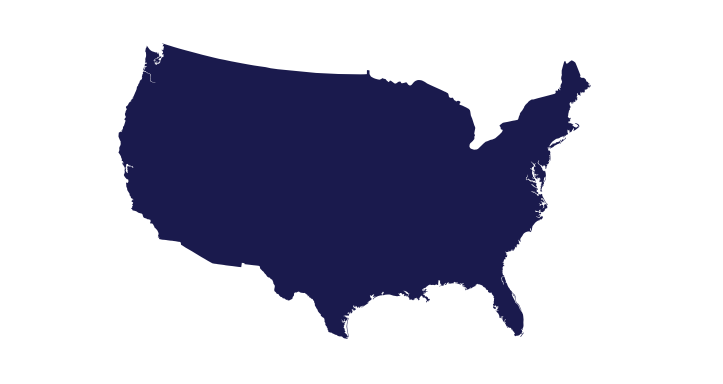

```mathematica
bounds = GeoBounds[LinguisticAssistant]
GeoGraphics[{GeoStyling[RGBColor[.1,.1,.3], Opacity[1]],Polygon[LinguisticAssistant]}, GeoRange->bounds, GeoBackground->RGBColor[1, 1,1]]
```

```mathematica
nfcEastTeams = {Entity["City",{"NewYork","NewYork","UnitedStates"}], Entity["City",{"Philadelphia","Pennsylvania","UnitedStates"}], Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}], Entity["City",{"Dallas","Texas","UnitedStates"}]}

nfcNorthTeams = {Entity["City",{"GreenBay","Wisconsin","UnitedStates"}], Entity["City",{"Chicago","Illinois","UnitedStates"}], Entity["City",{"Detroit","Michigan","UnitedStates"}], Entity["City",{"SaintPaul","Minnesota","UnitedStates"}]}
nfcSouthTeams = {Entity["City",{"Charlotte","NorthCarolina","UnitedStates"}], Entity["City",{"Atlanta","Georgia","UnitedStates"}], Entity["City",{"NewOrleans","Louisiana","UnitedStates"}],Entity["City",{"Tampa","Florida","UnitedStates"}]} 
nfcWestTeams = {LinguisticAssistant, LinguisticAssistant, LinguisticAssistant, LinguisticAssistant}

nfcEast=Table[EntityValue[nfcEastTeams[[i]], "Position"], {i, 1, 4}]
nfcNorth = Table[EntityValue[nfcNorthTeams[[i]], "Position"], {i, 1, 4}]
nfcSouth =  Table[EntityValue[nfcSouthTeams[[i]], "Position"], {i, 1, 4}]
nfcWest =  Table[EntityValue[nfcWestTeams[[i]], "Position"], {i, 1, 4}]
nfc = {nfcEast, nfcNorth, nfcWest, nfcSouth}
```

{New York City,Philadelphia,Washington,Dallas}

{Green Bay,Chicago,Detroit,Saint Paul}

{Charlotte,Atlanta,New Orleans,Tampa}

{San Francisco,Seattle,Phoenix,Saint Louis}

{GeoPosition[{40.6643,-73.9385}],GeoPosition[{40.0094,-75.1333}],GeoPosition[{38.9041,-77.0171}],GeoPosition[{32.7942,-96.7655}]}

{GeoPosition[{44.5134,-88.0158}],GeoPosition[{41.8376,-87.6818}],GeoPosition[{42.383,-83.1022}],GeoPosition[{44.9489,-93.1039}]}

{GeoPosition[{35.2087,-80.8307}],GeoPosition[{33.7629,-84.4227}],GeoPosition[{29.9728,-90.059}],GeoPosition[{27.9701,-82.4797}]}

{GeoPosition[{37.7599,-122.437}],GeoPosition[{47.6205,-122.351}],GeoPosition[{33.5722,-112.088}],GeoPosition[{38.6357,-90.2446}]}